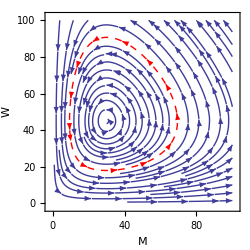

```mathematica
pp=StreamPlot[{.9*X-.02*X*Y, .02*X*Y-.6*Y},{X,0,100},{Y,0,100},StreamPoints->{{{{10,35},{Dashed,Red}},Automatic}},FrameLabel->{"M","W"},StreamScale->Medium,ImageSize->250]
```

```mathematica
Export["PredatorPreyPhasePlane.png", pp, ImageResolution->600]
```

PredatorPreyPhasePlane.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PredatorPreyPhasePlane.png"]]]
```

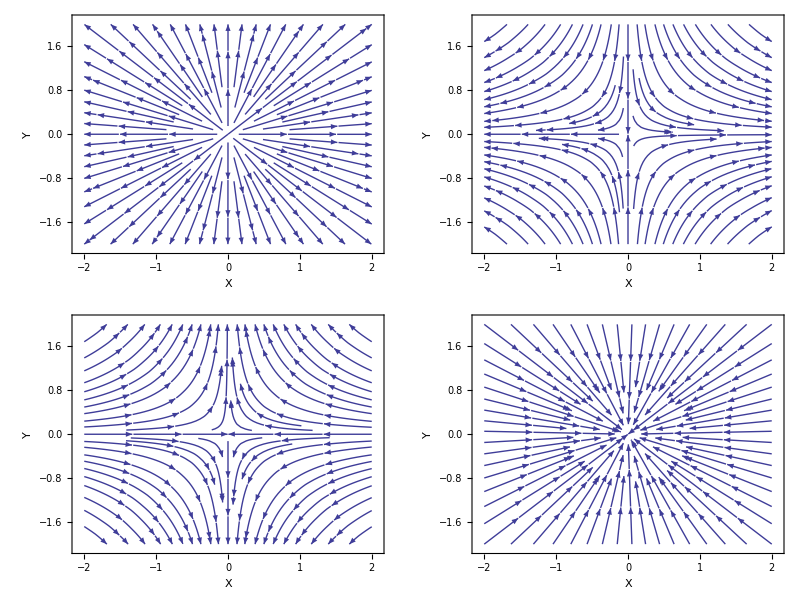

```mathematica
TableForm[{{StreamPlot[{X,Y},{X,-2,2},{Y,-2,2},FrameLabel->{"X","Y"},StreamScale->Medium,ImageSize->250],StreamPlot[{X,-Y},{X,-2,2},{Y,-2,2},FrameLabel->{"X","Y"},StreamScale->Medium,ImageSize->250]},{StreamPlot[{-X,Y},{X,-2,2},{Y,-2,2},FrameLabel->{"X","Y"},StreamScale->Medium,ImageSize->250],StreamPlot[{-X,-Y},{X,-2,2},{Y,-2,2},FrameLabel->{"X","Y"},StreamScale->Medium,ImageSize->250]}}]
```

```mathematica
d
```

d

```mathematica
Solve[0==a M - b M W && 0==g M W- d W, {M,W}]
```

{{M→0,W→0},{M→d/g,W→a/b}}

```mathematica
Solve[{x==7+y ,y==4}, {x,y}]
```

{{x→11,y→4}}

```mathematica
Eigenvalues[{{0,a},{0,-a}}]
```

{-a,0}